#### Inicialización

#### Para escribir la hora y los tiempos

```mathematica
paded[j_]:=StringJoin[Take[Characters[" "<>ToString[j]],-2] ]
zeropaded[j_]:=StringJoin[Take[Characters["0"<>ToString[j]],-2] ]
padedsec[j_]:=StringJoin[Take[Characters[" "<>ToString[j]],-5] ]
```

```mathematica
currenttime:=StringTake[DateString[],-8];
currentday:=StringTake[StringTake[DateString[],15],-11]
hms[s_]:={Floor[s/3600],Floor[(s-3600Floor[s/3600])/60],s-3600Floor[s/3600]-60.Floor[(s-3600Floor[s/3600])/60]};
strhm[s_]:=If[s<60,"<1m",If[hms[s]⟦1⟧==0,ToString[hms[s]⟦2⟧]<>"m",
ToString[hms[s]⟦1⟧]<>"h "<>paded[hms[s]⟦2⟧]<>"m"]];
strhms[ss_]:=Block[{s=Round[ss]},If[ss<0.01,"<"<>ToString[0.01]<>"s",If[ss<60,ToString[NumberForm[hms[ss]⟦3⟧,{4,2}]]<>"s",If[hms[s]⟦1⟧==0,ToString[hms[s]⟦2⟧]<>"m "<>ToString[Round[hms[s]⟦3⟧,1]]<>"s",ToString[hms[s]⟦1⟧]<>"h "<>paded[hms[s]⟦2⟧]<>"m "<>ToString[Round[hms[s]⟦3⟧,1]]<>"s"]]]];
strhmscolon[s_]:=If[s>100000,"?...",If[s<0.01,"0",zeropaded[hms[s]⟦1⟧]<>":"<>zeropaded[hms[s]⟦2⟧]<>":"<>zeropaded[Round[hms[s]⟦3⟧,1]]],"?..."];
```

#### Set current directory

```mathematica
SetDirectory[NotebookDirectory[]];
```

#### Sistema de ecuaciones iniciales en el estado estacionario

• Se expresan los valores de parámetros en forma exacta (5/10 en vez de 0.5 etc.), 
• Se calcula el tiempo que tardan los cálculos más largos, 
• Se “calcula” el índice de la solución real positiva (lo que puede ahorrar problemas cuando cambien las soluciones y la real positiva no sea la segunda), 
• Se simplifican las soluciones y se guardan en ficheros.

```mathematica
(*Ecuaciones en el equilibrio de C0 a C5 y S (llamada aquí C6)*)
0==-kon L T+koff C0+k3 DD;
0==-kon L T+(koff +w)C0;
0==-k2 TP P+(k2off+k3) DD;
0==k2 TP P-(k2off+k3) DD;
TTP=Solve[0==-DD (k2off+k3)+k2 (-DD+PT) TP,TP][[1,1]];
ecuaciones={
0==kon L T-(koff +w) C0,
0==-k2 TP P+k2off DD+w C0
};
TableForm[ecuaciones]
```

0==kon L T-C0 (koff+w)
0==DD k2off-k2 P TP+C0 w

#### Ecuación de L y gráfica de C0 vs LT en el estado estacionario

```mathematica
((koff+w) (LT-L))/(kon L)==TT-(LT-L)-(w (LT-L))/k3-(w (k2off+k3)(LT-L))/(k2 (k3 PT-w (LT-L)))
```

((-L+LT) (koff+w))/(kon L)==L-LT+TT-((-L+LT) w)/k3-((k2off+k3) (-L+LT) w)/(k2 (k3 PT-(-L+LT) w))

```mathematica
rs=Together[TT-(LT-L)-(w (LT-L))/k3-(w (k2off+k3)(LT-L))/(k2 (k3 PT-w (LT-L)))];
ls=((koff+w) (LT-L))/(kon L);
```

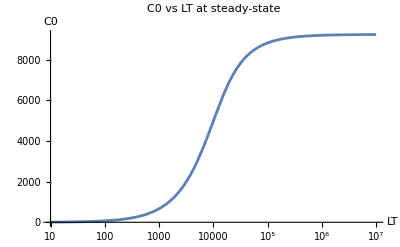

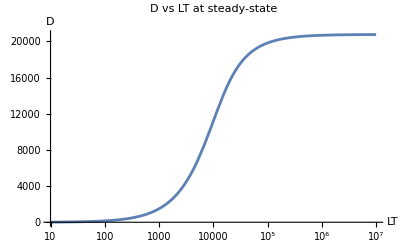

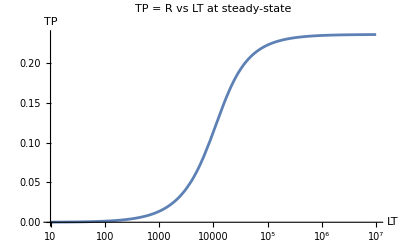

```mathematica
parametersFull={kon->10^-5,koff->5 10^-2,w->9 10^-2,k3->4 10^-2,k2->10^-1,k2off->5 10^-2,TT-> 3 10^4,PT->10^5};
Lequa=Collect[Numerator[rs]*Denominator[ls]-Numerator[ls]*Denominator[rs],L]//.parametersFull//N;
Leq[LT_]:=Solve[Lequa==0,L][[3,1,2]]//.parametersFull//N
LogLinearPlot[LT-Leq[LT],{LT,10^1,10^7},PlotLabel->"C0 vs LT at steady-state",AxesLabel->{"LT","C0"}]

Deq[LT_]:=Solve[Lequa==0,L][[3,1,2]]//.parametersFull//N
LogLinearPlot[(LT-Leq[LT]) w/k3/.parametersFull,{LT,10^1,10^7},PlotLabel->"D vs LT at steady-state",AxesLabel->{"LT","D"}]

TP[LT_]:= (w (k2off+k3)(LT-Leq[LT]))/(k2 (k3 PT-w (LT-Leq[LT])))//.parametersFull
LogLinearPlot[TP[LT],{LT,10^1,10^7},PlotLabel->"TP = R vs LT at steady-state",AxesLabel->{"LT","TP"}]
```

#### Ejemplo

```mathematica
maxR=FindMaximum[Re[TP[LT]],{LT,0,10^7}];
Emax=maxR[[1]];
lt50 = NSolve[TP[LT] == Emax/2//.parametersFull//N, LT];
EC50 = lt50[[1,1,2]];
TPec50=Re[TP[LT]/.LT->EC50];
Print["Emax = ", Emax]
Print["EC50 = ",EC50]
(*definición de C5 en el equilibrio en función de PT*)
(*gráfica de C5 en el equilibrio en función de PT*)
LogLinearPlot[{TP[LT],Emax,TPec50},{LT,1,10^7},PlotRange->All,PlotLabels->{"R","Emax","Emax/2"}]

ParametricPlot[{{lT,Re[TP[LT]//.LT->10^lT]},{lT,Emax},{lT,TPec50},{Log10[EC50],Re[TP[LT]//.LT->10^lT]}},{lT,0,7},AspectRatio->1/2,PlotRange->{All,{0,All}},PlotLabels->{"StyleBox[\"R\",FontSlant->\"Italic\"]","Emax","Emax/2","EC50"}]
```

Emax = 0.23592

EC50 = 10587.

-Graphics-

-Graphics-